```mathematica
SetDirectory["/Users/macbook/Dropbox/AWL/RoFSuP1_0"];
```

```mathematica
(*Force Mesh Parameters*)
```

```mathematica
x=50.0;       (*Position of force calculation in x if xdiv = 1*)
```

```mathematica
y=0.0;       (*Position of force calculation in y if ydiv = 1*)
```

```mathematica
zeta1 = 0.0;    (*Position of force calculation in zeta if zetadiv = 1*)
```

```mathematica
x0= 5.0;         (*Beam position x*)
```

```mathematica
y0=0.0;          (*Beam position y*)
```

```mathematica
xdiv=1;          (*Force calculation mesh divisions in x*)
```

```mathematica
ydiv = 1;        (*Force calculation mesh divisions in y*)
```

```mathematica
zetadiv = 100;  (*Force calculation mesh divisions in longitudinal direction*)
```

```mathematica
zetamin = 0;    (*Minimum value of longitudinal coordinate for force calculation*)
```

```mathematica
zetamax = 10;    (*Maximum value of longitudinal coordinate for force calculation*)
```

```mathematica
(*Beam Parameters*)
```

```mathematica
Energy = 10;       (*Energy of Particle in MeV*)
```

```mathematica
Mass = .5109989461;  (*Mass of Particle in MeV/c^2*)
```

```mathematica
gamma = Energy/Mass;   (*Lorentz Boost of Particle*)
```

```mathematica
beta = (1-1/gamma^2)^.5  ;
```

```mathematica
(*Cavity Parameters*)
```

```mathematica
Ep = 10;    (*Relative Permittivity of dielectric*)
```

```mathematica
Mu = 1;      (*Relative Permeability of dielectric*)
```

```mathematica
b= 10;    (*Distance from cavity center to dielectric*)
```

```mathematica
c=20;          (*Distance from cavity center to conducting wall (-c<y<c)*)
```

```mathematica
w= 100.0;      (*Width of Cavity (0<x<w)*)
```

```mathematica
(*Accuracy Parameters*)
```

```mathematica
NumModes = 100;    (*Number of frequcy modes in x*)
```

```mathematica
NumRoots = 100;      (*Number of frequency modes in y for each mode in x*)
```

```mathematica
Acc = .001;             (*Percision of root finder*)
```

```mathematica
x >>InputFile.txt
y >>> InputFile.txt
zeta1 >>> InputFile.txt
x0 >>> InputFile.txt
y0 >>> InputFile.txt
xdiv >>> InputFile.txt
ydiv >>> InputFile.txt
zetadiv >>> InputFile.txt
Ep >>> InputFile.txt
Mu >>> InputFile.txt
beta >>> InputFile.txt
b >>> InputFile.txt
c >>> InputFile.txt
w >>> InputFile.txt
NumModes >>> InputFile.txt
NumRoots >>> InputFile.txt
Acc >>> InputFile.txt
zetamin >>> InputFile.txt
zetamax >>> InputFile.txt
```

```mathematica
Run["./RoFSuP_1_0"]
```

0

```mathematica
Data =Import["FieldOutputFile.txt","Table"];
```

```mathematica
DataT = Transpose[Data];
```

```mathematica
zeta = DataT[[1]];
```

```mathematica
Fx = DataT[[2]];
```

```mathematica
Fy = DataT[[3]];
```

```mathematica
Fz = DataT[[4]];
```

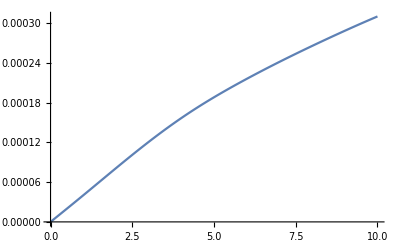

```mathematica
ListPlot[Thread[{zeta,Fx}],Joined->True]
```

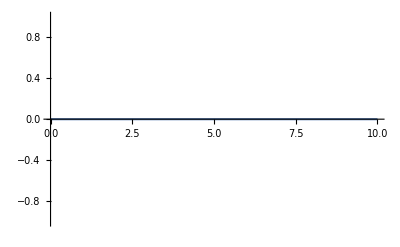

```mathematica
ListPlot[Thread[{zeta,Fy}],Joined->True]
```

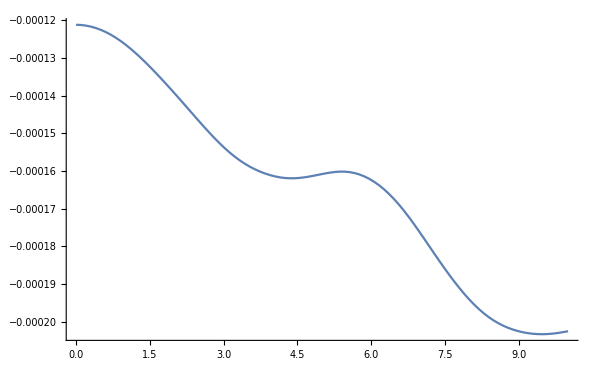

```mathematica
ListPlot[Thread[{zeta,Fz}],Joined->True]
```